## Numerical computation of the THE in a SkX

This section is an excerpt from one of the many codes written to study this problem of electron transport in a skyrmion crystal. The aim of this section is to explain the implementation part in brief detail followed by its code in an interactive manner. The computational software used is “WOLFRAM MATHEMATICA (student version)”. We begin with understanding the overall flow of this code by breaking it down to simple manageable steps . Later we elaborate each step in brief followed by a demonstration.

### Flow of this computation (Major blocks of this code)

Step 1: To construct a base lattice of points. In our case it will be a honeycomb lattice or graphene lattice.
Step 2: To construct the triple-Q texture on the base honeycomb lattice. This step will give us the SkX in which the electron transport happens.
Step 3: To isolate a unit cell and identify the NN of each site in the unit cell. This requires periodic boundary conditions.
Step 4: To construct the model Hamiltonian using the information gathered from Step 3. 
Step 5: To get the electronic band structure of this model Hamiltonian.
Step 6: To use the concept of berry phase and Kubo formula to calculate the transverse hall conductance.

#### Step 1 : Constructing a honeycomb lattice

-Graphics-
This the lattice we try to construct and it has 2 sub-lattices (A and B).  Each sub-lattice is a triangular lattice in itself. So we construct 2 triangular lattice separately and shift one of them to get the honeycomb lattice. The lattice translation vectors for triangular lattice will be,  OverVector[a_1] = (1, 0) and OverVector[a_2] = (1/2, (√3)/2).  We shift the sub-lattice number 2 by (0, 1/(√3)). This results in a honey comb lattice of side length of 1/(√3). (i.e, a  = 1/(√3)).

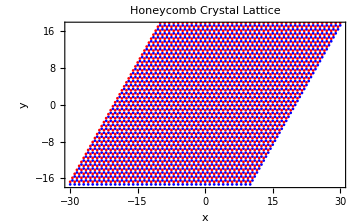

```mathematica
(* Honeycomb lattice construction - demonstration *)
(* Defining the lattice vector *)
a1={1, 0}; 
a2={1/2, (√3)/2}; 
n=20; (* Number of lattice points in each direction *)
(* generating the points in sublattices *)
sublattice1=Flatten[Table[a1*i+a2*j,{i,-n,n},{j,-n,n}],1];
sublattice2=Flatten[Table[a1*i+a2*j+{0,1/Sqrt[3]},{i,-n,n},{j,-n,n}],1];
(* combine both subblattices into single list called TriX*)
TriX = {};
Table[AppendTo[TriX,sublattice1[[i]]],{i,1,Length[sublattice1]}];
Table[AppendTo[TriX,sublattice2[[i]]],{i,1,Length[sublattice2]}];
(* Visualising the base honeycomb lattice *)
plot1 = ListPlot[sublattice1,PlotStyle->{Blue},PlotStyle->PointSize[Large]];
plot2 = ListPlot[sublattice2,PlotStyle->{Red},PlotStyle->PointSize[Large]];
Show[{plot1,plot2},
Frame->True,
FrameLabel->{"x","y"},
PlotLabel->"Honeycomb Crystal Lattice ",
 ImageSize->Medium,
BaseStyle->{FontSize->15}]
```

#### Step 2 : Constructing the triple - Q texture on the base honeycomb lattice

To achieve this we will need to define the direction of superposition of he spin helices. And the Q vectors in reciprocal space. The skyrmion lattice obtained using this texture is also a triangular lattice. So the size parameter defines the side length of the skyrmion. After achieving this we implement the triple-Q formula discussed in this thesis previously. A Neel skyrmion with zero helicity is constructed below.

```mathematica
(* Demonstration of triple-Q texture *)
(* Spin texture implimentation - Triple Q state of SkX*)
(* direction vectors of each spin helix in superposition *)
basisVectors ={{-1,0}, {1/2,-Sqrt[3]/2}, {1/2, Sqrt[3]/2}};(* skyrmion directions *)
size = 2; (* Size of skyrmion *)
(* Translation vectors of the skyrmions *)
T1 = {size+size/2,(√3)/2 size, 0};
T2 = {0, √3 size, 0};
T3 = {0,0,1};
(* volume and area are same as z direction is unit vector *)
volume = T1.(T2×T3); 
(* Reciprocal lattice vectors *)
B1 = (2 π)/volume(T2×T3);
B2 = (2 π)/volume(T3×T1);
(* Definitions for the spin texture *)
QVectors ={{B1[[1]],B1[[2]]}, {B2[[1]], B2[[2]]}, {B2[[1]], -B2[[2]]}};
(* Initail phase or epoch *)
epoch={Pi/3,Pi/3,Pi/3};
(* Spin texture *)
mxy [x_, y_] := Total[Table[(Sin[QVectors[[i]].{x,y}+epoch[[i]] ]) basisVectors[[i]],{i,1,3}]]
mz[x_, y_] :=  Total[Table[(Cos[QVectors[[i]].{x,y} +epoch[[i]]]),{i,1,3}]]
(* Spin texture function to get the 3D tuples *)
spins[x_, y_] := {N[mxy[x, y].{1,0}],N[ mxy[x, y].{0,1}], N[mz[x,y]]}

(* Visualization of the spin texture *)
(* Position vectors as 3D tuples *)
POSlist = Table[{TriX[[i]][[1]],TriX[[i]][[2]],0},{i,1,Length[TriX]}];
(* Generating the spin texture and normalizing them *)
texture =Table[spins[TriX[[i]][[1]], TriX[[i]][[2]]],{i, 1, Length[TriX]}]// N// Chop;
NORMtext = Table[texture[[i]]/Norm[texture[[i]]],{i,1,Length[texture]}];
(* Plotting the spin texture *)
(* colour of the spins is according to the z component *)
cylinders = Table[
{{ColorData["Rainbow"][Rescale[NORMtext[[i]][[3]],{-1,1}]],Cylinder[{POSlist[[i]]-NORMtext[[i]]/2,POSlist[[i]]},1/10]}},
{i,1,Length[TriX] }];
cones= Table[
{{ColorData["Rainbow"][Rescale[NORMtext[[i]][[3]],{-1,1}]],Cone[{POSlist[[i]],POSlist[[i]]+NORMtext[[i]]/2},1/5]}},
{i,1,Length[TriX] }];
texturePlot=Graphics3D[{cylinders,cones},Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->All,  ImageSize->Medium, Lighting->{{"Ambient",White}},ViewPoint->{0,0,1} ]
```

-Graphics3D-

#### Step 3: Isolating a unit cell and identify the NN of each site in the unit cell

The unit cell of a skyrmion is dictated by the SkX lattice translation vectors T1 and T2. The spins within the parallelogram formed by this vectors form the unit cell. The points on the parallel sides of the  isolated parallelogram will be identical so we consider only one from each parallel sides. On isolating the unit cell we use the spin texture at these points to identify the NN. Due to symmetry the NN of sub-lattice 1 will be in sub-lattice 2 and vice versa. We make use of this logic. The indexing of the points in unit cell  is the same order in which they are stored in the array.

{2,12,2}

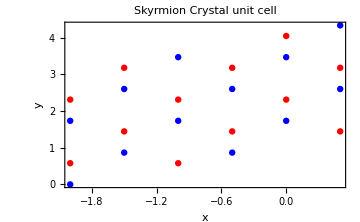

```mathematica
(* Demonstration - Isolating single skyrmion position as tuples *)
UNITcellS1={};
UNITcellS2={};
(* Bounds of unit cell *)
Xlow = -size;
Xhigh = size/2;
Ylow [x_]:=T1⟦2⟧/T1⟦1⟧(x + size)
Yhigh [x_]:=T1⟦2⟧/T1⟦1⟧(x + size) + Norm[T2]
(* Unitcell contribution from Sublattice 1 *)
For[i = 1, i<= Length[sublattice1],i++,
If[sublattice1[[i]][[1]]>=Xlow && sublattice1[[i]][[1]]<Xhigh , 
If[sublattice1[[i]][[2]]>=Ylow[sublattice1[[i]][[1]]] && sublattice1[[i]][[2]]<Yhigh[sublattice1[[i]][[1]]],
AppendTo[UNITcellS1, {sublattice1[[i]][[1]], sublattice1[[i]][[2]]}]]]]
(* Unitcell contribution from Sublattice 2 *)
For[i = 1, i<= Length[sublattice2],i++,
If[sublattice2[[i]][[1]]>=Xlow && sublattice2[[i]][[1]]<Xhigh , 
If[sublattice2[[i]][[2]]>=Ylow[sublattice2[[i]][[1]]] && sublattice2[[i]][[2]]<Yhigh[sublattice2[[i]][[1]]],
AppendTo[UNITcellS2, {sublattice2[[i]][[1]], sublattice2[[i]][[2]]}]]]]
(* Merging them to form a single array *)
UNITcell = {UNITcellS1, UNITcellS2};
UNITcell//Dimensions
(* Visualisint the isolated points in unit cell *)
plot3 = ListPlot[UNITcellS1,PlotStyle->{Blue}];
plot4 = ListPlot[UNITcellS2,PlotStyle->{Red}];
Show[plot3,plot4,Frame->True,PlotStyle->PointSize[0.3],FrameLabel->{"x","y"},PlotLabel->" Skyrmion Crystal unit cell ", ImageSize->Medium, BaseStyle->{FontSize->15}]
```

Here we begin with defining the conventions for the neighbours. Then we form the neighbour list. Where the index denotes which points neighbour it is. For e.g. To access the NN 2 from 3 point in sub lattice 1 we need to use the command “S1NN2[[3]]”. So we take point in one sub lattice then go to its neighbour position and then we search for the corresponding point’s index in the other sub lattice. We use the translation vectors as necessary. Using the translation vectors  ensures the periodicity in unit cell boundaries.

```mathematica
(* Neighbour table for Periodic Boundary condition Implimentation *)
(* Convention chosen for neighbour distances "L1N1 - sub Lattice 1 Neigbour 1" *)
L1N1 = {-1/2,-1/(2 √3)};
L1N2 = {0,1/(√3)};
L1N3 = {1/2,-1/(2 √3)};
L2N1 = {-1/2,1/(2 √3)};
L2N2 = {1/2,1/(2 √3)};
L2N3 = {0,-1/(√3)};
(* Convention chosen for Array names "S1NN1 - sub Lattice 1 Nearest Neigbour 1" *)
S1NN1 ={};
S1NN2 ={};
S1NN3 ={};
S2NN1 ={};
S2NN2 ={};
S2NN3 ={};
(* SUBLATTICE 1*)
For[i = 1, i<= Length[UNITcellS1], i++,
For[j=1,j<=Length[UNITcellS1], j++,
If[UNITcell[[2]][[j]]==UNITcell[[1]][[i]]+L1N1 ,
AppendTo[S1NN1, j],
(If[UNITcell[[2]][[j]] ==UNITcell[[1]][[i]]+L1N1+ {T1[[1]], T1[[2]]},
AppendTo[S1NN1, j],
If[UNITcell[[2]][[j]]==UNITcell[[1]][[i]]+L1N1+{T1[[1]], T1[[2]]}+{T2[[1]], T2[[2]]},
AppendTo[S1NN1, j]]])
]];]

For[i = 1, i<= Length[UNITcellS1], i++,
For[j=1,j<=Length[UNITcellS1], j++,
If[UNITcell[[2]][[j]]==UNITcell[[1]][[i]]+L1N2 ,
AppendTo[S1NN2, j],
(If[UNITcell[[2]][[j]] ==UNITcell[[1]][[i]]+L1N2- {T2[[1]], T2[[2]]},
AppendTo[S1NN2, j]])
]];]

For[i = 1, i<= Length[UNITcellS1], i++,
For[j=1,j<=Length[UNITcellS1], j++,
If[UNITcell[[2]][[j]]==UNITcell[[1]][[i]]+L1N3 ,
AppendTo[S1NN3, j],
If[UNITcell[[2]][[j]] ==UNITcell[[1]][[i]]+L1N3- {T1[[1]], T1[[2]]},
AppendTo[S1NN3, j],
If[UNITcell[[2]][[j]] ==UNITcell[[1]][[i]]+L1N3 + {T2[[1]], T2[[2]]},
AppendTo[S1NN3, j]]]
]];]

(* SUBLATTICE 2*)
For[i = 1, i<= Length[UNITcellS1], i++,
For[j=1,j<=Length[UNITcellS1], j++,
If[UNITcell[[1]][[j]]==UNITcell[[2]][[i]]+L2N1 ,
AppendTo[S2NN1, j],
(If[UNITcell[[1]][[j]] ==UNITcell[[2]][[i]]+L2N1- {T2[[1]], T2[[2]]},
AppendTo[S2NN1, j],
If[UNITcell[[1]][[j]]==UNITcell[[2]][[i]]+L2N1+{T1[[1]], T1[[2]]},
AppendTo[S2NN1, j]]])
]];]

For[i = 1, i<= Length[UNITcellS1], i++,
For[j=1,j<=Length[UNITcellS1], j++,
If[UNITcell[[1]][[j]]==UNITcell[[2]][[i]]+L2N2 ,
AppendTo[S2NN2, j],
(If[UNITcell[[1]][[j]] ==UNITcell[[2]][[i]]+L2N2- {T1[[1]], T1[[2]]},
AppendTo[S2NN2, j]])
]];]

For[i = 1, i<= Length[UNITcellS1], i++,
For[j=1,j<=Length[UNITcellS1], j++,
If[UNITcell[[1]][[j]]==UNITcell[[2]][[i]]+L2N3 ,
AppendTo[S2NN3, j],
(If[UNITcell[[1]][[j]] ==UNITcell[[2]][[i]]+L2N3+ {T2[[1]], T2[[2]]},
AppendTo[S2NN3, j]])
]];]
(* Printing the outputs *)
S1NN1
S1NN2
S1NN3
S2NN1
S2NN2
S2NN3
```

{11,1,2,12,3,4,5,6,7,8,9,10}

{1,2,8,3,4,5,6,7,12,9,10,11}

{4,5,6,2,8,9,10,11,1,7,12,3}

{9,4,12,1,2,3,10,5,6,7,8,11}

{2,3,5,6,7,8,9,10,11,12,1,4}

{1,2,4,5,6,7,8,3,10,11,12,9}

#### Step 4: Constructing the model Hamiltonian

We discuss the strong Hund’s coupling limit case. Initially we extract the spin profile from the skyrmion unit cell. We use these θ and ϕ values obtain the spin eigen vector  |χ^↑⟩. These vectors will be used in forming the inner products which will enter the matric as effecting hopping parameter. The set delayed form  and symbolic manipulation of MATHEMATICA is used in constructing the Hamiltonian matrix.

```mathematica
(* Spin texture or spin profile in a unit cell *)
spTEX = Table[spins[UNITcell[[i]][[j]][[1]],UNITcell[[i]][[j]][[2]]],{i, 1,2},{j,1, Length[UNITcellS1]}]//N//Chop;
(* Converting to Spherical Polar Coordinates *)
SpinPOLAR=CoordinateTransform["Cartesian"->"Spherical",spTEX]/.Indeterminate->0;
(* Collecting the theta and phi values *)
θ =Table[SpinPOLAR[[i]][[j]][[2]],{i, 1,2},{j,1, Length[UNITcellS1]}];
ϕ =Table[SpinPOLAR[[i]][[j]][[3]],{i, 1,2},{j,1, Length[UNITcellS1]}];
(* spin eigen vetors *)
KetArray = Table[{Cos[1/2 θ⟦i⟧[[j]]], Sin[1/2 θ⟦i⟧[[j]]] ⅇ^(ⅈ ϕ⟦i⟧[[j]])},{i, 1,2},{j,1, Length[UNITcellS1]}]//Chop;
KetArray// MatrixForm;
(* The conjugate vector of the spin texture |χ^↑⟩, ⟨χ^↑|:=|χ^↑⟩† *)
BraArray = Table[Conjugate[KetArray[[i]][[j]]],{i, 1,2},{j,1, Length[UNITcellS1]}];
BraArray// MatrixForm;
```

ArcTan::indet: Indeterminate expression ArcTan[0,0] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

Since the unit cell array first contains the entries from sub lattice 1 (SL_1), followed by sub lattice 2 (SL_2). Then the Hamiltonian matrix is of dimensions (N X N). Here N being total no of sites in unit cell. So it becomes into four blocks with hopping of an electron from a site in unit cell another . It is  explained in the picture below.
-Graphics-
In constructing the Hamiltonian we use the usual method of constructing a sparse matrix of appropriate dimensions (N X N) and replace the entries in them.

```mathematica
(* Constructing the Hamiltonian - demonstration *)
(* Parameters *)
t=1; 
(* general point in a reciprocal space *)
K[kx_, ky_] := {kx, ky}
(* Hamiltonian matrix *)
Hij[kx_, ky_] := Module[{hopingProduct,len},
len = Length[UNITcellS1];
hopingProduct = ConstantArray[0,{2Length[UNITcellS1],2Length[UNITcellS1]}];
For[i = 1, i<= len, i++,
hopingProduct[[i]][[S1NN1[[i]]+ len]] =t BraArray[[1]][[i]].KetArray[[2]][[S1NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].L1N1) ;
hopingProduct[[i]][[S1NN2[[i]]+ len]] =t BraArray[[1]][[i]].KetArray[[2]][[S1NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].L1N2)  ;
hopingProduct[[i]][[S1NN3[[i]] +len]] =t BraArray[[1]][[i]].KetArray[[2]][[S1NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].L1N3) ;
hopingProduct[[i+len]][[S2NN1[[i]]]] = t BraArray[[2]][[i]].KetArray[[1]][[S2NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].L2N1)  ;
hopingProduct[[i+len]][[S2NN2[[i]]]] = t BraArray[[2]][[i]].KetArray[[1]][[S2NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].L2N2)  ;
hopingProduct[[i+len]][[S2NN3[[i]]]] = t BraArray[[2]][[i]].KetArray[[1]][[S2NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].L2N3)  ;
];
hopingProduct
]
(* Checking if the hamiltonian is hermitian *)
ConjugateTranspose[Hij[2,2]]== Hij[2,2]
```

True

#### Step 5 : Electronic band structure Calculation

Now evaluate the Hamiltonian along the high symmetric path and plot the bands. The Reciprocal space for SkX is shown below and the Brillouin zone is the shaded blue  region. High symmetric Path is given as  Γ →  K →  M →  Γ.

```mathematica
(* Demonstration - band structure plot *)
Ev[kx_,ky_] := Sort[Eigenvalues[Hij[kx, ky]] ]
(* Collection of Eigen values along the irreducible path in the reciprocal space *)
d=25; (* step count *)
tabGK[n_]:=Table[Ev[k,k/(√3)][[n]],{k,0, Norm[B1]/2,Norm[B1]/(2 d)}];
tabKM[n_]:=Table[Ev[Norm[B1]/2,ky][[n]],{ky,Norm[B1]/(2 √3),0,-Norm[B1]/(√3 d)}];
tabMG[n_]:=Table[Ev[kx,0][[n]],{kx,Norm[B1]/2,0,-Norm[B1]/(2*0.87* d)}];
(* Visualizing Band structure plot *)
l1=Length[tabGK[1]];
l2=l1+Length[tabKM[1]];
l3=l2+Length[tabMG[1]];
customTicksX={{1,Style["Γ",Bold]},{l1,Style["K",Bold]},{l2,Style["M",Bold]},{l3,Style["Γ",Bold]}};
vl1=Graphics[{Dashed,Line[{{l1,-20},{l1,20}}]},AspectRatio->1];
vl2=Graphics[{Dashed,Line[{{l2,-20},{l2,20}}]},AspectRatio->1];
join[i_]:=Join[tabGK[i],tabKM[i],tabMG[i]]
bands:=Table[join[i],{i,1,2Length[UNITcellS1]}];
databands = bands;
```

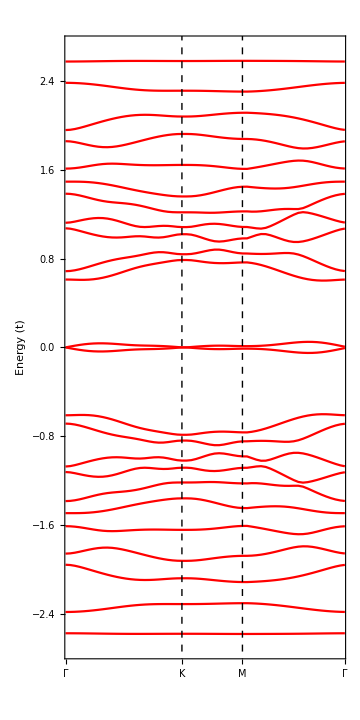

```mathematica
Show[ListLinePlot[databands,ImageSize->Medium,AspectRatio->1,FrameTicks->{{Automatic,None},{customTicksX,None}},Axes->False,Frame->True, PlotStyle->Red, FrameTicksStyle->Directive[Bold,Black]],vl1,vl2, BaseStyle->{FontSize->16}, FrameLabel->{"",Style["Energy (t)",Bold, Black]}, PlotRange->{{2,l3-1},{-2.7,2.7}}, AspectRatio->2,Background->White]
```

#### Step 6 : Calculate the transverse hall conductance

To calculate Hall conductance we first evaluate the Berry curvature for the bands in the Brillouin zone. To do we sample points from the Brillouin zone first. The generate the 3D band and berry curvature data for all the bands then this data is used to implement the Kubo formula.

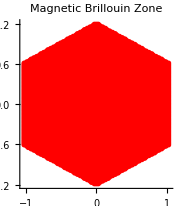

{9453,2}

```mathematica
(* Sampling the Brillouin zone *)
(*Side length of the hexagon*)
sideLength=Norm[B1]/(√3);
(*Define the hexagonal domain*)
hexagon=Polygon[Table[sideLength {Sin[2 π k/6],Cos[2 π k/6]},{k,6}]];
(*Distance between grid points*)
distance=0.02;
(*Generate a grid of points within the hexagon*)
kpoint=Select[Flatten[Table[{x,y},{x,-sideLength,sideLength,distance},
{y,-sideLength,sideLength,distance}],1],RegionMember[hexagon,#]&];
(*Display the hexagon and grid points*)
Show[
Graphics[{{EdgeForm[Black],FaceForm[],hexagon},{Red,PointSize[0.02],Point[kpoint]}}, ImageSize->Small, Axes->True, AxesStyle->Thick],PlotLabel->"Magnetic Brillouin Zone"]
kpoint//Dimensions
```

```mathematica
(* Berry Curvature demonstration *)
SortedEVectors[kx_, ky_]:= Module[{eigenvalues, eigenvectors, SEvalue, SEvector, SEvectorC},
{eigenvalues,eigenvectors}=Eigensystem[Hij[kx, ky]];
{SEvalue,SEvector}=Transpose[SortBy[Transpose[{eigenvalues,eigenvectors}],First]];
SEvectorC = SEvector//Chop;
For[i=1, i<=2*Length[UNITcell], i++,
SEvectorC[[i]]  = SEvectorC[[i]]/Norm[SEvectorC[[i]]];
];
SEvectorC// Chop
];
(* Derivatives definition *)
Hdx[kxval_, kyval_] := Module[{hopingProduct,len},
len =Length[UNITcellS1];
hopingProduct = ConstantArray[0,{2*Length[UNITcellS1],2*Length[UNITcellS1]}];
For[i = 1, i<= len, i++,
hopingProduct[[i]][[S1NN1[[i]]+ len]] =D[t BraArray[[1]][[i]].KetArray[[2]][[S1NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].L1N1),kx];
hopingProduct[[i]][[S1NN2[[i]]+ len]] =D[t BraArray[[1]][[i]].KetArray[[2]][[S1NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].L1N2),kx];
hopingProduct[[i]][[S1NN3[[i]] +len]] =D[t BraArray[[1]][[i]].KetArray[[2]][[S1NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].L1N3),kx];
hopingProduct[[i+len]][[S2NN1[[i]]]] = D[t BraArray[[2]][[i]].KetArray[[1]][[S2NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].L2N1),kx];
hopingProduct[[i+len]][[S2NN2[[i]]]] = D[t BraArray[[2]][[i]].KetArray[[1]][[S2NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].L2N2),kx];
hopingProduct[[i+len]][[S2NN3[[i]]]] = D[t BraArray[[2]][[i]].KetArray[[1]][[S2NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].L2N3),kx];];
hopingProduct/.{kx-> kxval, ky-> kyval}
]
Hdy[kxval_, kyval_] := Module[{hopingProduct,len},
len = Length[UNITcellS1];
hopingProduct = ConstantArray[0,{2*Length[UNITcellS1],2*Length[UNITcellS1]}];
For[i = 1, i<= len, i++,
hopingProduct[[i]][[S1NN1[[i]]+ len]] =D[t BraArray[[1]][[i]].KetArray[[2]][[S1NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].L1N1),ky];
hopingProduct[[i]][[S1NN2[[i]]+ len]] =D[t BraArray[[1]][[i]].KetArray[[2]][[S1NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].L1N2),ky];
hopingProduct[[i]][[S1NN3[[i]] +len]] =D[t BraArray[[1]][[i]].KetArray[[2]][[S1NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].L1N3),ky];
hopingProduct[[i+len]][[S2NN1[[i]]]] = D[t BraArray[[2]][[i]].KetArray[[1]][[S2NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].L2N1),ky];
hopingProduct[[i+len]][[S2NN2[[i]]]] = D[t BraArray[[2]][[i]].KetArray[[1]][[S2NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].L2N2),ky];
hopingProduct[[i+len]][[S2NN3[[i]]]] = D[t BraArray[[2]][[i]].KetArray[[1]][[S2NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].L2N3),ky];];
hopingProduct/.{kx-> kxval, ky-> kyval}
]
(* Berry connection for band *)
bconnection[kx_,ky_,bandindex_]:=Module[{sum,nket,newarray,dHx,dHy,otherev ,bandev,mket,ediff},
bandev=Ev[kx,ky][[bandindex]];
otherev = Delete[Ev[kx,ky],bandindex];
nket=SortedEVectors[kx,ky][[bandindex]];
mket=Delete[SortedEVectors[kx,ky],bandindex];
dHx=Hdx[kx,ky];
dHy=Hdy[kx,ky];
ediff[i_]:=(bandev-otherev[[i]]);
sum=Table[(-(Conjugate[nket].(dHx.mket[[i]]))*(Conjugate[mket[[i]]].(dHy.nket))+(Conjugate[nket].(dHy.mket[[i]]))*(Conjugate[mket[[i]]].(dHx.nket)))/ediff[i]^2,{i,1,Length[mket]}];
sum//Total//Im];
(* Function to evaluvate berry curvayure on a band *)
B[bandindex_]:= Flatten[Table[bconnection[kpoint[[j]][[1]], kpoint[[j]][[2]],bandindex],{j, 1, Length[kpoint]}]]
```

```mathematica
(* Sample plot of Berry curvature of Band 1 *)
berry1=B[1];
```

```mathematica
ListPlot3D[Table[{kpoint[[i]][[1]],kpoint[[i]][[2]],berry1[[i]]},{i,1,Length[kpoint]}],PlotRange->All, AxesLabel->{"x","y","Ω"}, BaseStyle->{FontSize->15, Black},Background->White]
```

-Graphics3D-

```mathematica
Total[berry1](2Pi)/(Length[kpoint]*(volume))
```

-1.0003

```mathematica
(* Calculating the band structure data for all bands *)
band3d[i_] :=Table[Ev[kpoint[[j]][[1]], kpoint[[j]][[2]]][[i]],{j,1,Length[kpoint]}]
bands =Flatten[ Table[Flatten[band3d[i]],{i, 1,2Length[UNITcellS1]}]];
bands//Dimensions
```

{18684}

```mathematica
(* Calculating the required berry curvature data for all the bands *)
Berry =Flatten[ Table[B[i],{i, 1, 2*Length[UNITcellS1]}]];
Berry//Dimensions
```

{18684}

```mathematica
(* Kubo formula implimentation *)
conductivity[ef_, KT_, bands_, berry_] := Module[{energies, bclist, term, result},
{energies,bclist}=Transpose[Select[Transpose[{bands,berry}],#[[1]]<=ef&]];
term = Table[bclist⟦i⟧/(1+ⅇ^((energies⟦i⟧-ef)/KT)),{i, 1, Length[energies]}];
result = Total[term];
result   //Chop
]
(* Parameters *)
Ef = Table[i,{i, -3,3, 1/100}];
Kt = 0.00000001;
(* evaluvating the hall conductivity *)
sigma = Table[{Ef[[i]],conductivity[Ef[[i]], Kt, bands, Berry]2Pi/(2 Length[UNITcellS1]*Length[kpoint]*(volume))},{i, 1, Length[Ef]}];
```

Set::shape: Lists {energies$198697,bclist$198697} and {} are not the same shape.

Set::shape: Lists {energies$198704,bclist$198704} and {} are not the same shape.

Set::shape: Lists {energies$198707,bclist$198707} and {} are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

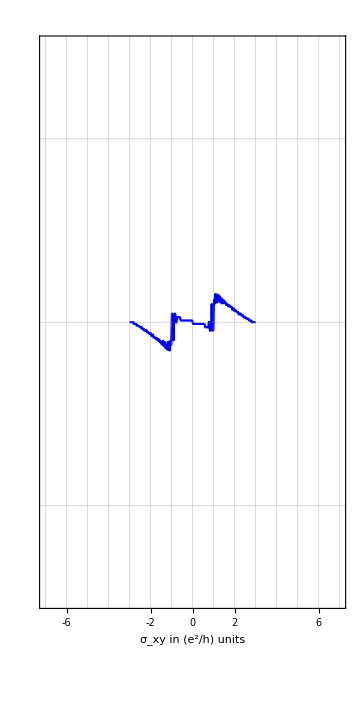

```mathematica
(* Visualising the quantised hall conductivity *)
customTicksX={{2,Style["2",Bold, Black]},{4,Style["4",Bold, Black]},{6,Style["6",Bold, Black]},{8,Style["8",Bold, Black]},{-2,Style["-2",Bold, Black]},{-4,Style["-4",Bold, Black]},{-6,Style["-6",Bold, Black]},{-8,Style["-8",Bold, Black]},{0,Style["0",Bold, Black]}};
sigmaplot = ListLinePlot[sigma , GridLines->{{-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8}, {-8,-6,-4,-2,0,2,4,6,8}},  Frame->True,BaseStyle->{FontSize-> 20},Background->White,ImageSize->Medium,FrameLabel->{"σ_xy in (e^2/h) units"},PlotRange->{{-7,7},{-3,3}},FrameTicks->{{None,None},{customTicksX,None}}, PlotStyle->Blue];
Show[sigmaplot,AspectRatio->2]
```

```mathematica
Export["/Users/satheeshdm/Desktop/January/MSc Thesis/Honeycomb model/54_sites.csv",sigma,"CSV"]
```

/Users/satheeshdm/Desktop/January/MSc Thesis/Honeycomb model/54_sites.csv